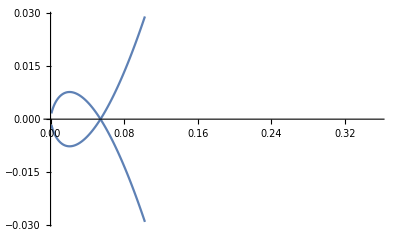

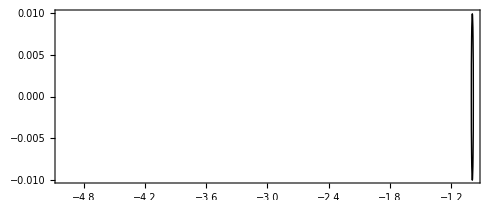

-Graphics-

```mathematica
RealPart[w_] := (44w^2+24)/(4w^6+53w^4+150w^2+36)
ImPart[w_] := (8w^3-66w)/(4w^6+53w^4+150w^2+36)
G1 =ListLinePlot[Table[{RealPart[x],ImPart[x]}, {x, -10, 10, 0.01}], PlotRange->{Automatic, Automatic}]
G2 = Graphics[Circle[{-1,0},0.01], PlotRange->{{-5,-1}, Automatic}, Frame->True, Axes->True]
Show[G1,G2]
```